# MapReduce in Mathematica

Frederico Meinberg

## Initialization

```mathematica
<<MapReduce`
```

Get::noopen: Cannot open "MapReduce`".

$Failed

## Examples

### Word count

The records are lists of words:

```mathematica
ClearAll[t,mr];
```

```mathematica
t[1]=BinPartition[StringSplit[StringReplace[ToLowerCase@ExampleData[{"Text","AeneidLatin"}],Except[WordCharacter]->" "]],1000];
```

Create a MapReduce function:

```mathematica
mr[1]=MapReduce[{"Map"->(1->Rule@@@Tally[{##}]&),"Reduce"->(BinRules[Join@@#2,Total@List[##]&]&)}]
```

Function[records$,SortBy[Join@@ParallelMap[(((Null&)[#1];#1)&)[Apply[BinRules[Join@@#2,Total[{##1}]&]&,#1,{1}]]&,(((Null&)[#1];#1)&)[BinPartition[(((Null&)[#1];#1)&)[BinRules[Join@@ParallelMap[Function[recordnode$,(((Null&)[#1];#1)&)[Apply[#1→(Flatten[{##1},{1}]&)@@#2&,BinRules[(((Null&)[#1];#1)&)[Apply[1→Apply[Rule,Tally[{##1}],{1}]&,recordnode$,{1}]]],{1}]]],BinPartition[records$,2]],Join]],2]]],First]]

```mathematica
t[2]=mr[1][t[1]];
```

```mathematica
Sort[First@t[2]]==Sort[Rule@@@Tally@Flatten@t[1]]
```

True

Add a combine step:

```mathematica
mr[2]=MapReduce[{"Map"->(1->Rule@@@Tally[{##}]&),"Combine"->(#1->{BinRules[Join@@#2,Total@List[##]&]}&),"Reduce"->(BinRules[Join@@#2,Total@List[##]&]&)}];
```

```mathematica
t[3]=mr[2][t[1]];
```

```mathematica
Sort[First@t[3]]==Sort[Rule@@@Tally@Flatten@t[1]]
```

True

### Temperatures

```mathematica
ClearAll[t,mr]
```

```mathematica
t[1]=Select[WeatherData["SanFrancisco" ,"Temperature" ,{2010}],FreeQ[#,Missing]&];
```

```mathematica
t[2]=RandomSample[t[1]];
```

Find the highest and lowest temperatures in each day:

```mathematica
mr[1]=MapReduce[{"Map"->(#1[[;;3]]->#2&),"Reduce"->{Max}}];
```

```mathematica
mr[2]=MapReduce[{"Map"->(#1[[;;3]]->#2&),"Reduce"->{Min}}];
```

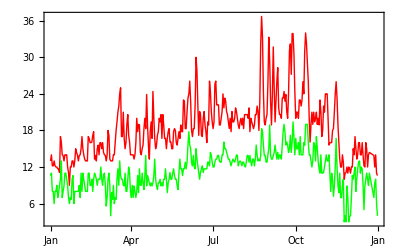

```mathematica
DateListPlot[{List@@@(mr[1][t[2]]),List@@@(mr[2][t[2]])},Joined->True,PlotStyle->{Red,Green,Blue},PlotRange->All]
```